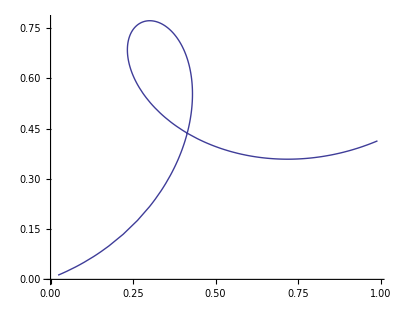

```mathematica
ParametricPlot[.3({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2}]
```

```mathematica
Round[Table[.3({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.1]
```

{{0,0},{0.1,0.1},{0.2,0.1},{0.3,0.2},{0.4,0.3},{0.4,0.4},{0.4,0.5},{0.4,0.6},{0.4,0.7},{0.4,0.7},{0.4,0.8},{0.3,0.8},{0.3,0.8},{0.2,0.7},{0.2,0.7},{0.2,0.7},{0.3,0.6},{0.3,0.5},{0.4,0.5},{0.4,0.4},{0.5,0.4},{0.6,0.4},{0.8,0.4},{0.9,0.4},{1.,0.4}}

```mathematica
StringJoin[("[NSValue valueWithPoint:NSMakePoint("<>ToString[#[[1]]]<>", "<>ToString[#[[2]]]<>")],\n")&/@Round[Table[.3({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3}),{t,-π/2,3π/2,π/12}],0.01]]
```

[NSValue valueWithPoint:NSMakePoint(0.02, 0.01)],
[NSValue valueWithPoint:NSMakePoint(0.13, 0.07)],
[NSValue valueWithPoint:NSMakePoint(0.23, 0.14)],
[NSValue valueWithPoint:NSMakePoint(0.31, 0.23)],
[NSValue valueWithPoint:NSMakePoint(0.37, 0.32)],
[NSValue valueWithPoint:NSMakePoint(0.41, 0.41)],
[NSValue valueWithPoint:NSMakePoint(0.43, 0.5)],
[NSValue valueWithPoint:NSMakePoint(0.43, 0.59)],
[NSValue valueWithPoint:NSMakePoint(0.41, 0.66)],
[NSValue valueWithPoint:NSMakePoint(0.39, 0.72)],
[NSValue valueWithPoint:NSMakePoint(0.35, 0.75)],
[NSValue valueWithPoint:NSMakePoint(0.31, 0.77)],
[NSValue valueWithPoint:NSMakePoint(0.28, 0.77)],
[NSValue valueWithPoint:NSMakePoint(0.25, 0.74)],
[NSValue valueWithPoint:NSMakePoint(0.23, 0.71)],
[NSValue valueWithPoint:NSMakePoint(0.24, 0.66)],
[NSValue valueWithPoint:NSMakePoint(0.26, 0.6)],
[NSValue valueWithPoint:NSMakePoint(0.3, 0.53)],
[NSValue valueWithPoint:NSMakePoint(0.36, 0.48)],
[NSValue valueWithPoint:NSMakePoint(0.44, 0.42)],
[NSValue valueWithPoint:NSMakePoint(0.53, 0.39)],
[NSValue valueWithPoint:NSMakePoint(0.64, 0.36)],
[NSValue valueWithPoint:NSMakePoint(0.76, 0.36)],
[NSValue valueWithPoint:NSMakePoint(0.87, 0.38)],
[NSValue valueWithPoint:NSMakePoint(0.99, 0.41)],

```mathematica
Simplify[.3({t/1.8+Cos[t],N[ Sin[t]]}.{{Cos[π/8],Sin[π/8]},{-Sin[π/8],Cos[π/8]}}+{.5,1.3})/.t->(-π/2+index(2π/count))]
```

{-0.0918711+(0.967484 index)/count+0.114805 Cos[(2 index π)/count]+0.277164 Sin[(2 index π)/count],0.289814+(0.400745 index)/count-0.277164 Cos[(2 index π)/count]+0.114805 Sin[(2 index π)/count]}